# RandomMetalPseudoSubgenre

Generate a new metal subgenre in the spirit of the many metal microgenres

## Definition

```mathematica
ClearAll[RandomMetalPseudoSubgenre];

Attributes[RandomMetalPseudoSubgenre]={Listable};

RandomMetalPseudoSubgenre[n_Integer]:=Table[RandomMetalPseudoSubgenre[],{i,1,n}];
RandomMetalPseudoSubgenre[UpTo[n_Integer]]:=Table[RandomMetalPseudoSubgenre[],{i,1,n}];

RandomMetalPseudoSubgenre[]:=Module[{
	absfirst={"new wave of","first wave of","second wave of"},
	first={"alternative","ambient","atmospheric","depressive","experimental","heavy","neo","nu",
		"old school","progressive","traditional"},
	(* ↓ Handle possibility of "black" and "blackened" together ↓ *)
	prefixes={"anarcho-","autonomous","avante-garde","biker","black","blackened","brutal","cavernous",
		"Celtic","chaotic","cosmic","crust","dark","death","dissonant","doom","drone",
		"electro","folk","forest","funeral","funk","garage","glam","gore","gothic","grind","groove",
		"hardcore","horror","indie","industrial","instrumental","interdimensional","math","melodic","minimal",
		"necro","neo-classical","noir","noise","pagan","pirate","post-","power","primitive","psychadelic","rap","raw",
		"sci-fi","slam","sludge","speed","stoner","symphonic","technical","thrash","Viking",
		"void","war","witch"},
	locs={"American","Appalachian","Arabic","Austrian","Brazillian","British","California","Chinese",
		"Dutch","Finnish","Florida","French","German","Greek","Hungarian","Icelandic","Iranian","Irish",
			"Latin","Midwest","Norwegian","NYC","Polish","Russian","Scandinavian","Slavic","Southern",
			"Swedish","Tampa","Ukranian"},
	suffixes={"crust","death","djent","doom","screamo","stench","thrash"},
	end={"core","death","doom","fusion","gaze","gothabilly","grind","grunge",(* "metal", *)
		" 'n' roll","psychobilly","punk",(* "rock", *)"sass","scape","thrash","violence","wave"},
	(* etc={"/","-"}, *)
	absrand,abs,firstrand,firstt,prerand,pres,locrand,nat,suffrand,suffs,endrand,endd,list1,list2,list3
},
	absrand=RandomInteger[{0,1}];
	abs=RandomSample[absfirst,absrand];

	firstrand=RandomInteger[{0,1}];
	firstt=RandomSample[first,firstrand];

	prerand=RandomInteger[{1,5}];
	pres=RandomSample[prefixes,prerand];

	locrand=RandomInteger[{0,1}];
	nat=RandomSample[locs,locrand];

	suffrand=RandomInteger[{1,2}];
	suffs=RandomSample[suffixes,suffrand];

	endrand=1;
	endd=RandomSample[end,endrand];

	(* Avoid things like "...thrash...thrash", "...death...death" etc. *)
	If[!DisjointQ[suffs,pres],pres=Complement[pres,suffs]];
	If[!DisjointQ[endd,pres],pres=Complement[pres,endd]];
	If[!DisjointQ[endd,suffs],suffs=Complement[suffs,endd]];

	(* StringReplace avoids things like post-- and anarcho-- *)
	list1=StringReplace[StringRiffle[pres," "],"--"->"-"];
	list2=StringJoin[If[abs!={},abs <> " ",""],If[firstt!={},firstt <> " ",""],If[nat!={},nat <> " ",""],list1];
	list2=StringJoin[If[abs!={},abs <> " ",""],If[nat!={},nat <> " ",""],If[firstt!={},firstt <> " ",""],list1];
	list3=StringJoin[list2," ",suffs,endd];
	list3=Capitalize[list3, "TitleCase"];
	list3=StringReplace[list3,{"- "->"-"}];
	(* ↑ handles "post- blah" and "anarcho- blah" ↑ *)

	Return[list3]
];
```

## Documentation

### Usage

RandomMetalPseudoSubgenre[]

generates a String consisting of one random (probably-fictitious) metal subgenre.

RandomMetalPseudoSubgenre[n]

generates a List of n subgenres.

RandomMetalPseudoSubgenre[UpTo[n]]

is the same as RandomMetalPseudoSubgenre[n].

RandomMetalPseudoSubgenre[{n_1,n_2,…}]

generates an n_1×n_2×⋯ array of subgenres.

### Details & Options

In the above, the arguments n and n_i must be integers.

RandomMetalPseudoSubgenre automatically threads over lists of integers.

RandomMetalPseudoSubgenre uses RandomInteger and RandomSample under the hood to create as much randomness as possible, but duplicates may still exist (see "Possible Issues" below).

## Examples

### Basic Examples

Generate a random (probably-fictitious) metal subgenre:

```mathematica
RandomMetalPseudoSubgenre[]
```

Second Wave of Atmospheric Cavernous Death Gore Sci-Fi Doomthrash 'n' Roll

### Scope

Here are five random (probably-fictitious) metal subgenres:

```mathematica
list1=RandomMetalPseudoSubgenre[5]
```

{Old School Noise Garage Djentfusion,Melodic Depressive Screamowave,Second Wave of Norwegian Doom Funeral Glam Noise Crustdjentthrash,New Wave of Ukranian Interdimensional Thrashscreamogothabilly,French Melodic War Symphonic Dissonant Neo-Classical Stenchwave}

It may be easier to read as a Column:

```mathematica
Column[list1]
```

Old School Noise Garage Djentfusion
Melodic Depressive Screamowave
Second Wave of Norwegian Doom Funeral Glam Noise Crustdjentthrash
New Wave of Ukranian Interdimensional Thrashscreamogothabilly
French Melodic War Symphonic Dissonant Neo-Classical Stenchwave

Using UpTo provides a different way to get five random (probably-fictitious) metal subgenres:

```mathematica
RandomMetalPseudoSubgenre[UpTo[5]]
```

{Alternative Autonomous Indie Garage Sci-Fi Crustscreamopunk,First Wave of Heavy Funeral Djentdeath,Experimental Indie Sci-Fi Autonomous Crustfusion,First Wave of Finnish Traditional Raw Stenchdoom,Brazillian Heavy Minimal Groove Blackened Math Screamogrind}

Here is an array of random (probably-fictitious) metal subgenres:

```mathematica
list2=RandomMetalPseudoSubgenre[{1,2,3}]
```

{{New Wave of Irish Neo Primitive Necro Autonomous Folk Thrash 'n' Roll},{Second Wave of Nu Raw Thrashpunk,Second Wave of Crust Screamostench 'n' Roll},{New Wave of Ambient Depressive Screamo Garage Stenchdeathdoom,New Wave of Experimental Gore Industrial Interdimensional Glam Drone Doompsychobilly,California Noir Dark Chaotic Crustdoom}}

The nesting is easier to visualize using Grid with the Frame->All option:

```mathematica
Grid[list2,Frame->All]
```

New Wave of Irish Neo Primitive Necro Autonomous Folk Thrash 'n' Roll |  | 
Second Wave of Nu Raw Thrashpunk | Second Wave of Crust Screamostench 'n' Roll | 
New Wave of Ambient Depressive Screamo Garage Stenchdeathdoom | New Wave of Experimental Gore Industrial Interdimensional Glam Drone Doompsychobilly | California Noir Dark Chaotic Crustdoom

### Possible Issues

RandomMetalPseudoSubgenre[n] returns unevaluated when n is any data type not mentioned in "Usage":

```mathematica
RandomMetalPseudoSubgenre[a]
```

RandomMetalPseudoSubgenre[a]

```mathematica
RandomMetalPseudoSubgenre[3.2]
```

RandomMetalPseudoSubgenre[3.2]

```mathematica
RandomMetalPseudoSubgenre[Sqrt[7]]
```

RandomMetalPseudoSubgenre[√7]

```mathematica
RandomMetalPseudoSubgenre["wolfram"]
```

RandomMetalPseudoSubgenre[wolfram]

RandomMetalPseudoSubgenre uses RandomInteger and RandomSample under the hood to create as much randomness as possible. For small samples, this is generally enough to avoid duplicates:

```mathematica
t1=RandomMetalPseudoSubgenre[50];
```

```mathematica
t1==DeleteDuplicates[t1]
```

True

Even so, duplicates may still exist in larger examples:

```mathematica
t2=RandomMetalPseudoSubgenre[5000];
```

```mathematica
t2==DeleteDuplicates[t2]
```

False

```mathematica
cc=Counts[t2];
cc[[Select[Range[Length[cc]],Values[cc][[#]]>1&]]]
```

<|Second Wave of Neo-Classical Thrashsass→2|>

### Neat Examples

While all of the examples are neat, some stand out more than others. For example, sometimes, you get really long subgenre names:

```mathematica
long=RandomMetalPseudoSubgenre[]
```

First Wave of Midwest Alternative Chaotic Stoner Screamo Groove Symphonic Djentdoompsychobilly

```mathematica
StringLength[long]
```

94

And sometimes, the subgenre names are really short:

```mathematica
short=RandomMetalPseudoSubgenre[]
```

Screamodeath

```mathematica
StringLength[short]
```

12

On average, however, the lengths of the subgenre names tend to be more average. Experimental evidence suggests that the Mean and Median of the subgenre name lengths are both around 50:

```mathematica
N@Mean[StringLength[RandomMetalPseudoSubgenre[1000]]]
```

50.684

```mathematica
Median[StringLength[RandomMetalPseudoSubgenre[1000]]]
```

51

To make metal seem more academic, you can test the Mean/Median hypothesis by using StringLength on longer and longer lists of subgenres. This yields a pair of datasets (where x is the length of the subgenre list and y is the Mean/Median of the corresponding list's string lengths) which seem to support the hypothesis.

Here is a plot of the corresponding Mean data:

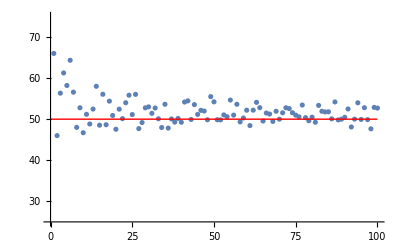

```mathematica
means=Table[{n,N@Mean[StringLength[RandomMetalPseudoSubgenre[n]]]},{n,1,max1=100}];
ListPlot[means,Epilog->{Red,Line[{{0,50},{max1,50}}]},PlotRange->{Automatic,{25,75}}]
```

And here is one for the Median data:

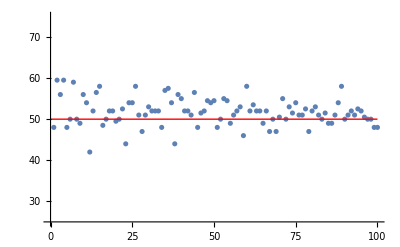

```mathematica
meds=Table[{n,N@Median[StringLength[RandomMetalPseudoSubgenre[n]]]},{n,1,max2=100}];
ListPlot[meds,Epilog->{Red,Line[{{0,50},{max2,50}}]},PlotRange->{Automatic,{25,75}}]
```

The trend can be summarized by taking the Mean of the means and the Median of the medians. Again, the results are very close to 50:

```mathematica
Mean[means[[All,2]]]//N
```

51.8493

```mathematica
Median[meds[[All,2]]]//N
```

52.

## Source & Additional Information

### Contributed By

Christopher Stover

### Keywords

music

metal

genre

metal music

subgenre

random

heavy metal

### Categories

3D Visualization |  Accessibility
 Accessing External Services & APIs |  Associations
 Astronomical Computation & Data |  Background & Scheduled Tasks
 Calculus |  Calling External Programs
 Cloud & Deployment |  Cloud Functions & Deployment
 Code as Data |  Color Processing
 Computational Geometry |  Computation on Graphs
 Computer Vision |  Control Objects
 Core Language & Structure |  Creating Form Interfaces & Apps
 Cryptography |  Cultural Data
 Data Manipulation & Analysis |  Data Structures
 Data Transforms and Smoothing |  Data Visualization
 Date & Time |  Decorations
 Differential Geometry |  Dimension Reduction
 Discrete Mathematics |  Dynamic Interactivity Language
 Engineering Data & Computation |  Error Handling
 Expressions |  External Interfaces & Connections
 External Language Interfaces |  File Operations
 Financial Data & Computation |  Front End Utilities
 Functional Programming |  Function Visualization
 Games |  Geographic Data and Entities
 Geographic Data & Computation |  Geographic Visualization
 Geometric Region Properties |  Geometric Transforms
 Geometry |  Graph Construction & Representation
 Graph Properties & Measurements |  Graphs & Networks
 Graph Visualization |  Handling Arrays of Data
 Higher Mathematical Computation |  Image Filtering & Neighborhood Processing
 Image Processing & Analysis |  Images
 Importing and Exporting |  Interactive Manipulation
 Iterated Maps & Fractals |  Just For Fun
 Knowledge Representation & Natural Language |  Layout & Tables
 Life Sciences & Medicine: Data & Computation |  Linguistic Data
 List Manipulation |  Logic & Boolean Algebra
 Low-Level Notebook Programming |  Machine Learning
 Maps & Cartography |  Mathematical Functions
 Matrices and Linear Algebra |  Molecular Structure & Computation
 Natural Language Processing |  Neural Networks
 Notebook Basics |  Notebook Document Generation
 Notebook Documents & Presentation |  Notebook Formatting & Styling
 Number Theory |  Numeric Approximation
 Optimization |  Parallel Computing
 Persistent Storage |  Physics & Chemistry: Data and Computation
 Plane Geometry |  Polynomial Algebra
 Precollege Education |  Presentations with the Wolfram System
 Probability & Statistics |  Programming Utilities
 Random Stuff |  Real & Complex Analysis
 Recreational Math |  Repository Tools
 RepositoryTools |  Rules & Patterns
 Scientific and Medical Data & Computation |  Scientific Data Analysis
 Segmentation Analysis |  Sequence Analysis
 Shortcuts and Idioms |  Signal Processing
 Social, Cultural & Linguistic Data |  Social Data
 Solid Geometry |  Sound & Video
 Statistical Data Analysis |  String Manipulation
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Text Analysis
 Text Manipulation |  Theorem Proving
 Time-Related Computation |  Time Series Processing
 Topology |  Tuning & Debugging
 Units & Quantities |  User Interface Construction
 Viewers and Annotation |  Visualization & Graphics
 Weather Data |  Web Operations
 Wolfram Physics Project |  Wolfram System Setup
 Working with Paclets |

### Related Symbols

RandomInteger

RandomSample

### Related Resource Objects

RandomPseudoSymbolName

RandomText

RandomString

### Source/Reference Citation

Source, reference or citation information

### Links

Wikipedia–Heavy metal music

Wikipedia–Heavy metal genres

Wikipedia–Extreme metal

Metal Wiki–Fandom

Wikipedia–Microgenre

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

There are several other notable metal genre prefixes that could have gone into the lists used herein; however, some prefixes deemed either "trivial" or "obscene" were omitted.

There is a great deal of musical knowledge built in to the Wolfram Language. As a starting point, one can check the entities listed under the "Music" subsection at Guide: Cultural Data.

## Submission Notes

Additional information for the reviewer.